# CTQW

```mathematica
Get[NotebookDirectory[]<>"../Kernel/init.m"] (*Load QuantumWalks package*)

Print["Last update: "<>DateString[{"Day"," ","MonthName"," ","Year"}]]
```

Last update: 25 February 2026

## Routines’ details and usage examples

## BuildAdjacencyMatrix[gridData, connectionVectors]

constructs the adjacency matrix of the graph defined by the grid geometry using an O(1) lookup search. This matrix dictates the allowed transitions between nodes.

It takes the following arguments:

gridData: An Association containing the coordinate basis and mapping (e.g., generated by GenerateRectangleBasis).

connectionVectors: (Optional) A list of vectors defining the allowed jumps. By default, it assumes nearest neighbors in a 2D square lattice: {{1, 0}, {-1, 0}, {0, 1}, {0, -1}}.

### Usage example

Build the adjacency matrix for a 3x3 rectangular grid (Lx=2, Ly=2):

```mathematica
grid=GenerateRectangleBasis[2,2];adjMatrix=BuildAdjacencyMatrix[grid];
```

Visualize the adjacency matrix structure:

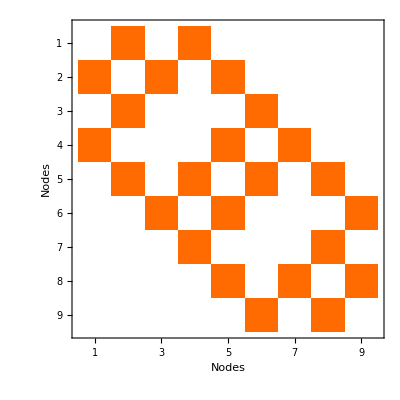

```mathematica
MatrixPlot[adjMatrix,FrameLabel->{"Nodes","Nodes"}]
```

## CTQWHamiltonian[gridData, gamma, connectionVectors]

constructs the continuous-time quantum walk (CTQW) Hamiltonian H = -γ L, where L = D - A is the graph Laplacian (D being the degree diagonal matrix and A the adjacency matrix).

It takes the following arguments:

gridData: An Association defining the geometry.

gamma: (Optional) The hopping factor γ. Defaults to 1.0.

connectionVectors: (Optional) A list of jump vectors. Defaults to nearest neighbors: {{1, 0}, {-1, 0}, {0, 1}, {0, -1}}.

### Usage example

Construct the Hamiltonian for the previous grid with a hopping factor of 0.5:

```mathematica
grid=GenerateRectangleBasis[2,2];
H=CTQWHamiltonian[grid,0.5]
```

SparseArray[…]

Verify that the Hamiltonian is a symmetric matrix:

```mathematica
SymmetricMatrixQ[H]
```

True

Check the dimensions of the Hamiltonian (9 nodes in a 3x3 grid):

```mathematica
Dimensions[H]
```

{9,9}